```mathematica
palindrome3[x_Integer]:= If[PalindromeQ[palindrome3[x]], Print[x],palindrome3[x]+IntegerReverse[palindrome3[x]]]
```

```mathematica
palindrome3[19]
```

110

```mathematica
Module[{llrev,ll=NestWhileList[(FromDigits@Reverse[IntegerDigits[#]]+#)&,19,Reverse@IntegerDigits[#]=!=IntegerDigits[#]&,1,50]},
llrev=Riffle[ll,Style[FromDigits[Reverse[IntegerDigits[#]]]]&/@ll];
If[Reverse@IntegerDigits[ll[[-1]]]==IntegerDigits[ll[[-1]]],ll[[-1]]=Style[ll[[-1]],"Label"];llrev[[-1]]=Style[llrev[[-1]],"Label"]]]
```

121

```mathematica
palindrome4[x_Integer]:=NestWhileList[(IntegerReverse[#]+#)&,x,Reverse@IntegerDigits[#]=!=IntegerDigits[#]&,1,50]
```

```mathematica
palindrome4[39]
```

{39,132,363}

```mathematica
palindrome5[x_Integer]:=BaseForm[NestWhileList[(IntegerReverse[#]+#)&,x,Reverse@IntegerDigits[#]=!=IntegerDigits[#]&,1,50],2]
```

```mathematica
palindrome5[39]
```

{100111_2,10000100_2,101101011_2}

```mathematica
IntegerDigits[palindrome5[39],2]
```

IntegerDigits[{100111_2,10000100_2,101101011_2},2]

```mathematica
BaseForm[780,2]
```

1100001100_2

```mathematica
IntegerDigits[%65,2]
```

{1,1,0,0,0,0,1,1,0,0}

```mathematica
IntegerDigits[{Subscript["100111", "2"],Subscript["10000100", "2"],Subscript["101101011", "2"]},2]
```

{{1,0,0,1,1,1},{1,0,0,0,0,1,0,0},{1,0,1,1,0,1,0,1,1}}

```mathematica
palindrome6[x_Integer]:=IntegerDigits[NestWhileList[(IntegerReverse[#]+#)&,x,Reverse@IntegerDigits[#]=!=IntegerDigits[#]&,1,50],2]
```

```mathematica
palindrome6[39]
```

{{1,0,0,1,1,1},{1,0,0,0,0,1,0,0},{1,0,1,1,0,1,0,1,1}}

```mathematica
palindrome7[x_Integer]:=ArrayPlot[IntegerDigits[NestWhileList[(IntegerReverse[#]+#)&,x,Reverse@IntegerDigits[#]=!=IntegerDigits[#]&,1,50],2],Background->GrayLevel[0.9]]
```

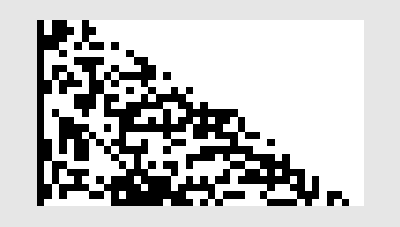

```mathematica
palindrome7[89]
```

### Initialization

```mathematica
palindrome8[x_Integer,y_Integer,z_Integer]:=ArrayPlot[PadLeft[IntegerDigits[NestWhileList[(IntegerReverse[#]+#)&,x,Reverse@IntegerDigits[#]=!=IntegerDigits[#]&,1,y],z]]]
listPalindrome[x_Integer,y_Integer]:=Column[NestWhileList[(IntegerReverse[#]+#)&,x,Reverse@IntegerDigits[#]=!=IntegerDigits[#]&,1,y]]
countPalindrome[x_Integer,y_Integer]:=Length[NestWhileList[(IntegerReverse[#]+#)&,x,Reverse@IntegerDigits[#]=!=IntegerDigits[#]&,1,y]]-1
finalPalindrome[x_Integer,y_Integer,z_Integer]:={palindrome8[x,y,z],listPalindrome[x,y],countPalindrome[x,y]}
repPalindrome[x_Integer,y_Integer,z_Integer]:=ArrayPlot[PadLeft[IntegerDigits[NestList[(IntegerReverse[#]+#)&,x,y],z]]]
```

```mathematica
listRepPalindrome[x_Integer,y_Integer]:=Column[NestList[(IntegerReverse[#]+#)&,x,y]]
```

### Program

```mathematica
finalPalindrome[196,100,2]
```

{-Graphics-,196
887
1675
7436
13783
52514
94039
187088
1067869
10755470
18211171
35322452
60744805
111589511
227574622
454050344
897100798
1794102596
8746117567
16403234045
70446464506
130992928913
450822227944
900544455998
1800098901007
8801197801088
17602285712176
84724043932847
159547977975595
755127757721546
1400255515443103
4413700670963144
8827391431036288
17653692772973576
85191620502609247
159482241005228405
664304741147513356
1317620482294916822
3603815405135183953
7197630720180367016
13305261530450734933
47248966933966985264
93507933867933969538
177104867844767940077
947154635293536341848
1795298270686072793597
9749270977546801719568
18408442064004592449047
92502871604050616929528
175095833209091234750057
925153265399993573340628
1751196640799987135692157
9264161958699957602603728
17537224026299926194218357
92918473189299188236491928
175837936477498486373973857
934217310162393261013712428
1758434620324786522027424867
9442681822581660752291773438
17786453745152322604573635887
96640091285774647759309104658
182280281681549295517528109327
906182107397142240703710191608
1712373124704184482497411473217
8836114272647029296571625205388
17671139534403958504034349321776
85383533877444544434477942439447
159876958854887988978955775977805
668656536414767878767414635656756
1326313072829535757534829271313622
3589444802113893332894111974449853
7178889593228875666877224058899706
13258878097456662332665448018788423
45747659181913285659330927106673654
91385319354816681317562845302348408
171869639709643252636224690693706727
899477035806065888888571598630674898
1797953072701241777777132207161449896
8787394689723559555548553279865047867
16474800379447118011108106559729985745
71233793175007298122189281057030833206
131467596250025596244378551114170566423
456132667661181469687074071166866330554
911166336322351940474038252333632562208
1713431572655604770948087405557266223327
8946658200210652579438861471120017566498
17893315300422394267788614031240046132996
87816479304635435956564863353640397472867
164643958609270772803130816807280794934745
712083455691979390834439093880187654281206
1314265912473067781768877187859384208661423
4555933937312655599557549065463126404285554
9111757983526301209015109021025263797681108
17123625957151502418030218042061517695252227
89348885628667526499233299462576693647884398
178697760268335052998466598925153376306768796
876565363941686582894131498175687238374565667
1643130837774473154788262996461373387738131345
7074449215608204801780891870975118165118444806
13158897331226320592562872742059146230247889513
44757771534490515617290699271561508443627774644,100}

```mathematica
Manipulate[finalPalindrome[x,y,z],{{x,10,"initial value(click enter after input)"},ControlType-> InputField},{{y,1,"max number of iterations"},1,200,1,Appearance-> "Labeled"},{{z,2,"Base"}, 2,10,1, ControlType-> PopupMenu}]
```

```mathematica
repPalindrome[794,50,2]
```

-Graphics-

```mathematica
listRepPalindrome[794,50]
```

794
1291
3212
5335
10670
18271
35552
61105
111221
233332
466664
933328
1756667
9423238
17746487
96211258
181422527
906646708
1714293317
8848217488
17695345976
85649705647
160300500305
663305503366
1326611006732
3702612172963
7395324335036
13700658570973
51608244171704
92325388452319
183650876804648
1030059554861029
10231744114361330
13548085259074531
27095180517159062
53190352025318134
96371704050627269
192644309091344638
1029087499994790929
10320062499942600130
13420687499368602431
26841373898847204862
53681648788684519724
96473197477469138359
191856393954948275828
1020429243414341934019
10124820677557771174220
12371938453135374016321
24732985806270857933642
49366961613531716857384
97742823327063333823778